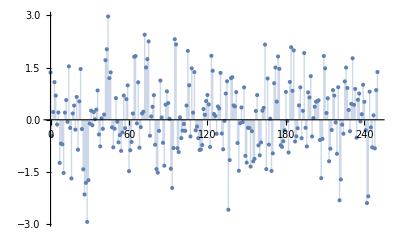

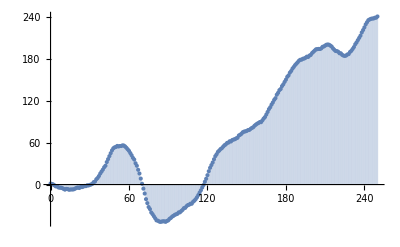

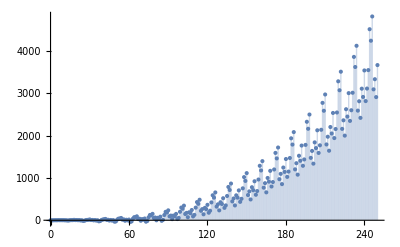

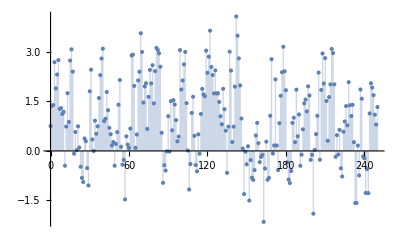

```mathematica
RandomFunction[ARMAProcess[{.1,.2},{.3,-.2},1],{0,250}];
ListPlot[%,Filling->Axis]

RandomFunction[ARIMAProcess[{-.7},2,{.2},1],{0,250}];
ListPlot[%,Filling->Axis]

RandomFunction[SARIMAProcess[{.4},1,{-1.3},{12,{.7,.3},2,{.7,-.3}},1],{0,250}];
ListPlot[%,Filling->Axis]

RandomFunction[FARIMAProcess[{.1},.45,{.2},1],{0,250}];
ListPlot[%,Filling->Axis]
```